# 2D First-Passage time

## Drift towards the equilibrium at (x, xh) = (0, 0) with an absorbing boundary at xh=1. Initial condition is a wide distribution which narrows on approach to the fixed point.

## Write down the nondimensionalized Fokker-Planck equation

```mathematica
FP=λ*D[xh*P[x, xh], x]+D[xh*P[x, xh], xh]-κ*D[x*P[x, xh],xh]+λ*D[P[ x, xh],{x,2}]+D[P[x, xh],{xh,2}]
```

P[x,xh]+xh P^(0,1)[x,xh]-x κ P^(0,1)[x,xh]+P^(0,2)[x,xh]+xh λ P^(1,0)[x,xh]+λ P^(2,0)[x,xh]

## Choose the parameter values

```mathematica
λs = {0.02, 0.05, 0.1,0.2, 0.5};
κs = {0.1, 0.2,0.5, 1, 2};
params = Flatten[Table[{λ->l, κ->k}, {l, λs}, {k, κs}], 1]
legend =  Flatten[Table["λ="<>ToString[l]<>"; "<> "κ="<>ToString[k], {l, λs},{k, κs}], 1];
```

{{λ→0.02,κ→0.1},{λ→0.02,κ→0.2},{λ→0.02,κ→0.5},{λ→0.02,κ→1},{λ→0.02,κ→2},{λ→0.05,κ→0.1},{λ→0.05,κ→0.2},{λ→0.05,κ→0.5},{λ→0.05,κ→1},{λ→0.05,κ→2},{λ→0.1,κ→0.1},{λ→0.1,κ→0.2},{λ→0.1,κ→0.5},{λ→0.1,κ→1},{λ→0.1,κ→2},{λ→0.2,κ→0.1},{λ→0.2,κ→0.2},{λ→0.2,κ→0.5},{λ→0.2,κ→1},{λ→0.2,κ→2},{λ→0.5,κ→0.1},{λ→0.5,κ→0.2},{λ→0.5,κ→0.5},{λ→0.5,κ→1},{λ→0.5,κ→2}}

## Set up the mesh, boundary conditions, and initial condition

#### Choose the same initial width for every parameter set: the one with the largest s.s. width in x

```mathematica
Table[1/(2κ)+((1+κ) λ)/(2κ)/.p, {p, params}]
```

{5.11,2.56,1.03,0.52,0.265,5.275,2.65,1.075,0.55,0.2875,5.55,2.8,1.15,0.6,0.325,6.1,3.1,1.3,0.7,0.4,7.75,4.,1.75,1.,0.625}

```mathematica
{{1/(2κ)+((1+κ) λ)/(2κ),1/2},{1/2,(1+κ)/2}}/.params[[21]]
```

{{7.75,1/2},{1/2,0.55}}

#### Boundary condition at x*=1, y* = 1

#### Also choose initial width for the steady-state width of each parameter pair

```mathematica
ystars = Table[1, 25]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
xf=20;
icPos = {5, 5};
icVar = {{1/(2κ)+((1+κ) λ)/(2κ),1/2},{1/2,(1+κ)/2}}/.params[[21]] 
ic0 = N[Table[PDF[MultinormalDistribution[icPos,icVar], {x, xh}], {i, params}]];(*ic0 : Choose widest s.s. distribution of the parameter values*)
icSS = N[Table[PDF[MultinormalDistribution[icPos,{{1/(2κ)+((1+κ) λ)/(2κ),1/2},{1/2,(1+κ)/2}}/.p], {x, xh}], {p, params}]];
(*icSS : Choose s.s. distribution width for each of the parameter values*)
bcs = Table[{P[-xf, xh]==0,
           P[xf, xh]==0,
           P[x, xf]==0,
           P[x, ystar]==0
}, {ystar,ystars}]

Needs["NDSolve`FEM`"]
meshes=Table[ToElementMesh[Rectangle[{-xf, ystar}, {xf, xf}],MaxCellMeasure->0.025 ], {ystar, ystars}]
```

{{7.75,1/2},{1/2,0.55}}

{{P[-20,xh]==0,P[20,xh]==0,P[x,20]==0,P[x,1]==0},{P[-20,xh]==0,P[20,xh]==0,P[x,20]==0,P[x,1]==0},{P[-20,xh]==0,P[20,xh]==0,P[x,20]==0,P[x,1]==0},{P[-20,xh]==0,P[20,xh]==0,P[x,20]==0,P[x,1]==0},{P[-20,xh]==0,P[20,xh]==0,P[x,20]==0,P[x,1]==0},{P[-20,xh]==0,P[20,xh]==0,P[x,20]==0,P[x,1]==0},{P[-20,xh]==0,P[20,xh]==0,P[x,20]==0,P[x,1]==0},{P[-20,xh]==0,P[20,xh]==0,P[x,20]==0,P[x,1]==0},{P[-20,xh]==0,P[20,xh]==0,P[x,20]==0,P[x,1]==0},{P[-20,xh]==0,P[20,xh]==0,P[x,20]==0,P[x,1]==0},{P[-20,xh]==0,P[20,xh]==0,P[x,20]==0,P[x,1]==0},{P[-20,xh]==0,P[20,xh]==0,P[x,20]==0,P[x,1]==0},{P[-20,xh]==0,P[20,xh]==0,P[x,20]==0,P[x,1]==0},{P[-20,xh]==0,P[20,xh]==0,P[x,20]==0,P[x,1]==0},{P[-20,xh]==0,P[20,xh]==0,P[x,20]==0,P[x,1]==0},{P[-20,xh]==0,P[20,xh]==0,P[x,20]==0,P[x,1]==0},{P[-20,xh]==0,P[20,xh]==0,P[x,20]==0,P[x,1]==0},{P[-20,xh]==0,P[20,xh]==0,P[x,20]==0,P[x,1]==0},{P[-20,xh]==0,P[20,xh]==0,P[x,20]==0,P[x,1]==0},{P[-20,xh]==0,P[20,xh]==0,P[x,20]==0,P[x,1]==0},{P[-20,xh]==0,P[20,xh]==0,P[x,20]==0,P[x,1]==0},{P[-20,xh]==0,P[20,xh]==0,P[x,20]==0,P[x,1]==0},{P[-20,xh]==0,P[20,xh]==0,P[x,20]==0,P[x,1]==0},{P[-20,xh]==0,P[20,xh]==0,P[x,20]==0,P[x,1]==0},{P[-20,xh]==0,P[20,xh]==0,P[x,20]==0,P[x,1]==0}}

{ElementMesh[{{-20.,20.},{1.,20.}},{QuadElement[<30613>]}],ElementMesh[{{-20.,20.},{1.,20.}},{QuadElement[<30613>]}],ElementMesh[{{-20.,20.},{1.,20.}},{QuadElement[<30613>]}],ElementMesh[{{-20.,20.},{1.,20.}},{QuadElement[<30613>]}],ElementMesh[{{-20.,20.},{1.,20.}},{QuadElement[<30613>]}],ElementMesh[{{-20.,20.},{1.,20.}},{QuadElement[<30613>]}],ElementMesh[{{-20.,20.},{1.,20.}},{QuadElement[<30613>]}],ElementMesh[{{-20.,20.},{1.,20.}},{QuadElement[<30613>]}],ElementMesh[{{-20.,20.},{1.,20.}},{QuadElement[<30613>]}],ElementMesh[{{-20.,20.},{1.,20.}},{QuadElement[<30613>]}],ElementMesh[{{-20.,20.},{1.,20.}},{QuadElement[<30613>]}],ElementMesh[{{-20.,20.},{1.,20.}},{QuadElement[<30613>]}],ElementMesh[{{-20.,20.},{1.,20.}},{QuadElement[<30613>]}],ElementMesh[{{-20.,20.},{1.,20.}},{QuadElement[<30613>]}],ElementMesh[{{-20.,20.},{1.,20.}},{QuadElement[<30613>]}],ElementMesh[{{-20.,20.},{1.,20.}},{QuadElement[<30613>]}],ElementMesh[{{-20.,20.},{1.,20.}},{QuadElement[<30613>]}],ElementMesh[{{-20.,20.},{1.,20.}},{QuadElement[<30613>]}],ElementMesh[{{-20.,20.},{1.,20.}},{QuadElement[<30613>]}],ElementMesh[{{-20.,20.},{1.,20.}},{QuadElement[<30613>]}],ElementMesh[{{-20.,20.},{1.,20.}},{QuadElement[<30613>]}],ElementMesh[{{-20.,20.},{1.,20.}},{QuadElement[<30613>]}],ElementMesh[{{-20.,20.},{1.,20.}},{QuadElement[<30613>]}],ElementMesh[{{-20.,20.},{1.,20.}},{QuadElement[<30613>]}],ElementMesh[{{-20.,20.},{1.,20.}},{QuadElement[<30613>]}]}

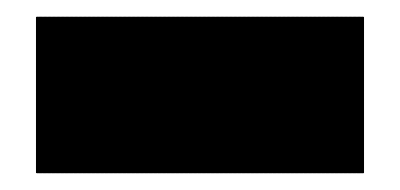

```mathematica
meshes[[1]]["Wireframe"]
```

## Calculate the probability distribution and the flux through the boundary

```mathematica
NDSolverParams[param_, ic_, bc_, mesh_] :=Module[{N},
N = NDSolve[Join[{(FP/. param)==-ic}, bc],
                                   P,Element[{x, xh}, mesh], 
Method->"FiniteElement"];
Return[(P/.N[[1]])];
]
```

```mathematica
(*solsSS=MapThread[NDSolverParams, {params, icSS, bcs, meshes}];*)
solsIc0=MapThread[NDSolverParams, {params, ic0, bcs, meshes}];
```

```mathematica
(*fluxSS = Table[Derivative[0,1][sol],{sol, solsSS}];*)
fluxIc0 = Table[Derivative[0,1][sol],{sol, solsIc0}];
```

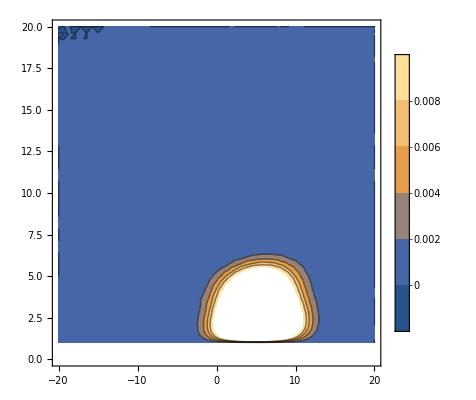

```mathematica
(*cSS =ContourPlot[solsSS[[1]][x, xh], {x, -xf, xf}, {xh, 0, xf}, PlotLegends->Automatic, PlotRange->{-0.01, 0.01}];*)
cIc0 =ContourPlot[solsIc0[[1]][x, xh], {x, -xf, xf}, {xh, 0, xf}, PlotLegends->Automatic, PlotRange->{-0.01, 0.01}];
(*Show[cSS]*)
Show[cIc0]
```

```mathematica
(*XSS = MapThread[#1[x,#2]&,{fluxSS,ystars}];*)
XIc0 =MapThread[#1[x,#2]&,{fluxIc0,ystars}];
```

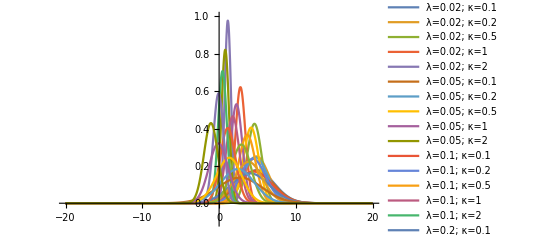

```mathematica
Plot[XSS, {x, -xf, xf}, PlotRange->{-0.1, 1}, PlotLegends->legend]
```

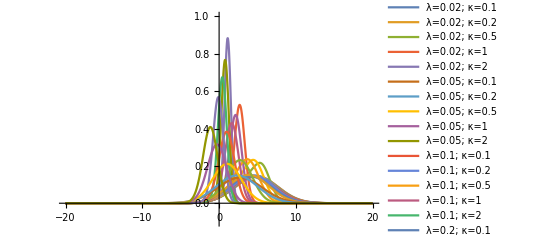

```mathematica
Plot[XIc0, {x, -xf, xf}, PlotRange->{-0.1, 1}, PlotLegends->legend]
```

```mathematica
normsSS = Table[NIntegrate[xp, {x, -10, 15}, WorkingPrecision->10], {xp, XSS}]
meansSS= Table[NIntegrate[xp*x, {x, -10, 15}, WorkingPrecision->10], {xp, XSS}]
secondSS = Table[NIntegrate[xp*x*x, {x, -10, 15}, WorkingPrecision->10], {xp, XSS}];
varsSS= secondSS-meansSS^2
diffSS = varsSS/meansSS;
```

{1.003114428,1.00384229,1.000637964,0.9965011283,0.9988544717,1.003072579,1.003805392,1.001607817,0.999698324,1.000875341,1.003001644,1.003732836,1.00244873,1.001426824,1.000897614,1.002855513,1.003548224,1.003045074,1.001967587,0.9974546243,1.002382336,1.00281487,1.002266925,0.9986198334,0.9820696351}

{4.919464231,4.895815056,4.594931724,2.804775618,1.146552668,4.774228215,4.714175271,4.179117134,2.292720741,0.8050781342,4.534731612,4.421334033,3.657099299,1.796409347,0.4444043018,4.064829762,3.867035005,2.877615651,1.153089558,-0.06894008388,2.719371819,2.386932385,1.273977572,-0.06741485625,-1.05320268}

{5.0542587,2.4738191,0.87281301,0.4391894,0.17087922,5.237228,2.5787473,0.94792611,0.57132401,0.239427242,5.5543509,2.7777161,1.1680068,0.73963001,0.323009985,6.2285542,3.2369383,1.6102808,0.993430974,0.462555494,8.48545133,4.82734124,2.68795165,1.55904993,0.849441826}

```mathematica
normsIc0 = Table[NIntegrate[xp, {x, -10, 15}, WorkingPrecision->10], {xp, XIc0}]
meansIc0= Table[NIntegrate[xp*x, {x, -10, 15}, WorkingPrecision->10], {xp, XIc0}]
secondIc0 = Table[NIntegrate[xp*x*x, {x, -10, 15}, WorkingPrecision->10], {xp, XIc0}];
varsIc0 = secondIc0-meansIc0^2
diffIc0 = varsIc0/meansIc0;
```

{1.002929777,1.003357152,0.9994959448,0.9977160403,0.9669518493,1.002918638,1.003384076,1.000840301,1.000177938,0.9864893053,1.002885931,1.003365937,1.001760518,1.001436646,0.9956067721,1.002788482,1.003246411,1.002353835,1.001547598,0.9960672944,1.002382336,1.002615661,1.00152754,0.997535249,0.9803260255}

{4.917311326,4.885704117,4.192215555,2.405049077,0.9920746615,4.771936081,4.696061287,3.747393672,1.961059071,0.696559506,4.532234825,4.393121304,3.235775457,1.50889251,0.3630343617,4.062224811,3.826920601,2.496654193,0.8974205305,-0.1417125733,2.719371819,2.339544913,0.9827921816,-0.3027267491,-1.16337196}

{7.6677829,7.5160782,4.3533448,1.1871519,0.411847218,7.65921744,7.3369385,3.7409894,1.1102186,0.407385363,7.66725441,7.13202598,3.4104752,1.12951387,0.44726387,7.75785554,6.94879671,3.29901695,1.24383767,0.548714428,8.48545133,7.24742032,3.68448435,1.64744854,0.948773542}

```mathematica
grid = Flatten[Table[{l, s}, {l, λs}, {s, κs}], 1];
params
```

{{λ→0.02,κ→0.1},{λ→0.02,κ→0.2},{λ→0.02,κ→0.5},{λ→0.02,κ→1},{λ→0.02,κ→2},{λ→0.05,κ→0.1},{λ→0.05,κ→0.2},{λ→0.05,κ→0.5},{λ→0.05,κ→1},{λ→0.05,κ→2},{λ→0.1,κ→0.1},{λ→0.1,κ→0.2},{λ→0.1,κ→0.5},{λ→0.1,κ→1},{λ→0.1,κ→2},{λ→0.2,κ→0.1},{λ→0.2,κ→0.2},{λ→0.2,κ→0.5},{λ→0.2,κ→1},{λ→0.2,κ→2},{λ→0.5,κ→0.1},{λ→0.5,κ→0.2},{λ→0.5,κ→0.5},{λ→0.5,κ→1},{λ→0.5,κ→2}}

```mathematica
(*normArraySS = ArrayReshape[normsSS, {5, 5}];
varArraySS = ArrayReshape[varsSS, {5, 5}];
meanArraySS = ArrayReshape[meansSS, {5, 5}];
diffArraySS = ArrayReshape[diffSS, {5, 5}];*)
normArrayIc0 = ArrayReshape[normsIc0, {5, 5}];
varArrayIc0 = ArrayReshape[varsIc0, {5, 5}];
meanArrayIc0 = ArrayReshape[meansIc0, {5, 5}];
diffArrayIc0 = ArrayReshape[diffIc0, {5, 5}];
```

```mathematica
cf[x_]:=Blend[{{-2, Red},{ 1,White},{5,Blue}}, x]
```

```mathematica
xticks = Transpose[{{1, 2, 3, 4, 5}, λs}];
yticks = Transpose[{{1, 2, 3, 4, 5}, κs}];
```

```mathematica
ArrayPlot[varArraySS, ColorFunction->(Blend[{{-1, Red},{ 0,White},{1,Blue}},#]&), PlotLegends->{Placed[BarLegend[Automatic,None,LegendLabel->"var(x)"],Right]}, FrameTicks->{xticks, yticks}, DataReversed->True, FrameLabel->{λ, κ}]

ArrayPlot[ArrayReshape[Table[Blend[{{-2, Red},{ 0,White},{5,Blue}}, i],{i,Flatten[meanArraySS]}], {5,5}], PlotLegends->{Placed[BarLegend[{cf[#]&,{-2, 5}},LegendLabel->"mean(x)"],Right]}, FrameTicks->{xticks, yticks}, DataReversed->True, FrameLabel->{λ, κ}]

ArrayPlot[normArraySS, ColorFunction->(Blend[{White,Blue},#]&), PlotLegends->{Placed[BarLegend[Automatic,Automatic,LegendLabel->"norm(e(x))"],Right]}, FrameTicks->{xticks, yticks}, DataReversed->True, FrameLabel->{λ, κ}]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
ArrayPlot[varArrayIc0, ColorFunction->(Blend[{{-1, Red},{ 0,White},{1,Blue}},#]&), PlotLegends->{Placed[BarLegend[Automatic,None,LegendLabel->"var(x)"],Right]}, FrameTicks->{xticks, yticks}, DataReversed->True, FrameLabel->{λ, κ}]

ArrayPlot[ArrayReshape[Table[Blend[{{-2, Red},{ 0,White},{5,Blue}}, i],{i,Flatten[meanArrayIc0]}], {5,5}], PlotLegends->{Placed[BarLegend[{cf[#]&,{-2, 5}},LegendLabel->"mean(x)"],Right]}, FrameTicks->{xticks, yticks}, DataReversed->True, FrameLabel->{λ, κ}]

ArrayPlot[normArrayIc0, ColorFunction->(Blend[{White,Blue},#]&), PlotLegends->{Placed[BarLegend[Automatic,Automatic,LegendLabel->"norm(e(x))"],Right]}, FrameTicks->{xticks, yticks}, DataReversed->True, FrameLabel->{λ, κ}]
```

-Graphics-

-Graphics-

-Graphics-